## check: (R, θ, ϕ)

```mathematica
(pt=RandomPoint[Ball[{0,0,0},10],5000])//Graphics3D@*Point
```

-Graphics3D-

```mathematica
{pt1,pt2}=GatherBy[pt,Last[#]<0&];
```

```mathematica
polarDistcells=With[{cent=Mean@pt},
{
(x↦coordTrans[x-cent])/@pt1,
(x↦coordTrans[x-cent])/@pt2
}
];
```

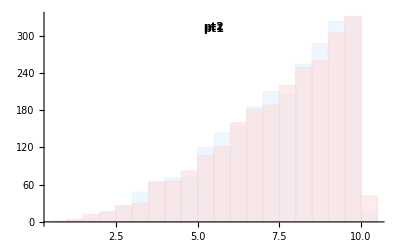

```mathematica
Histogram[polarDistcells[[All,All,1]],ChartStyle->{LightBlue,LightRed,LightGreen},ChartLabels->{Style["pt1",Bold,Black],
Style["pt2",Bold,Black]},PlotRange->All]
```

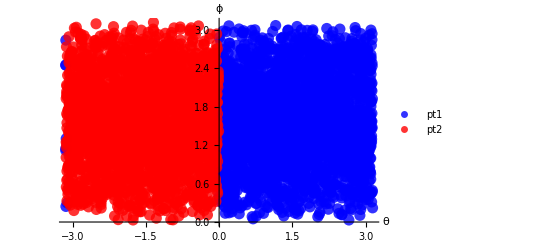

```mathematica
ListPlot[polarDistcells[[All,All,{3,2}]],
PlotStyle->{{PointSize[0.02],Opacity[0.8],Blue},{PointSize[0.02],Opacity[0.8],Red},Green},
PlotLegends->{"pt1","pt2"},AxesLabel->(Style[#,Black,19]&/@{"θ","ϕ"}),AxesStyle->{{Black,15},{Black,15}}]
```

## Saved Res

```mathematica
polarRep={{{{26.104979149168223,1.875401046371192,-1.6343716785840128},{21.51056262712276,1.9655376181772442,-1.8900554273653245},{18.876130973676013,1.5281000282022261,-1.5959948402018582},{25.239394288785608,0.9246648083930008,-1.9317653947973656},{27.925592902689502,2.347015946999316,-1.9005857942608269},{26.433947600596042,1.6745348906844826,-2.4457985304057397},{25.61363086377186,1.954990634979657,-0.7309711768183466},{33.61561643900919,2.629613220776911,-1.8450530354334185},{19.332997572120224,1.1877482409322007,-1.0844836063472374},{19.6794112414442,1.8251275209310478,-0.8943957556078577},{19.398394981768565,2.1284339223228073,-2.141301017914067},{30.1012063869064,2.1407461445631797,-0.5783188770272392},{22.396404488791667,1.283758768716869,-2.440674179595921},{30.76643159045068,1.3188851201601577,-2.6580303934652023},{13.64114357038733,2.0860966720798078,-1.5175406931403608},{13.550869591735946,1.2785009926741049,-1.1516663990932305},{21.109046902302463,2.5355164121676506,-1.740020007050216},{20.595198073158365,1.6716364302673925,-2.6399660400647176},{22.454341937128504,2.196089042657152,-2.5697314973852654},{30.00606389803596,2.4973949426205175,-2.5630942454660794},{13.355603066895497,2.281751542057127,-2.076587577199766},{16.96377601861925,1.0270802650364612,-2.5700495752303816},{25.190705723522246,1.6973832324444191,-2.821921798299784},{30.042607759093453,2.3296171162332184,-0.3685045665253262},{21.95008973910995,0.763269067883848,-2.6730019881070035},{16.645848687747087,1.3883779442075115,-2.7096489351599296},{24.586375849997314,1.9915961368617887,-0.2638596579772287},{28.152260843040438,1.0826266460764713,-2.903963145495319},{33.7509457637432,1.8251773484589726,-2.961437898361542},{7.493005087496823,1.913130714407531,-2.383470000081553},{15.569208530328758,0.8265639553821509,-0.43756231146369734},{18.83117160522856,2.147332097193148,-0.3124560222030053},{9.25642787928425,1.2637508690896584,-0.4518910625854371},{10.724811633524675,2.4199438523107353,-0.5749728373123696},{20.88407414205058,1.1017850743854505,-2.987841797604997},{26.795438931933514,2.131542522311959,-3.0598452975146193},{17.145823565844154,2.3672569433941133,3.1293262702594555},{6.054736738021214,0.4489638318140117,0.05598874206389568},{22.113680133464296,2.595659375215907,0.012808371769737084},{10.673510477247847,2.8641359131400743,2.7384115168063374},{16.000033668655718,1.1633209550473318,3.0634288551224174},{16.01044848871765,0.88778543603398,0.09249564715490673},{13.499282818498266,1.6095713552982542,2.9817432978509006},{14.299173647660872,1.5764123396970755,0.15072506702638508},{4.367607586032304,2.2481440124752394,1.180193200226424},{14.929730803624814,2.328939847733384,0.29454116132927277},{24.007428003826266,0.8491015558792542,2.9660702704726503},{23.531969367226313,0.6650003859178827,0.2896301958490499},{27.207047483522846,0.2932332376548009,0.7135144564972108},{30.294200702154683,1.698038406935244,0.2060201556777483},{27.852751777068253,1.365547306134169,0.26520075209452904},{17.427603267041945,0.711120215750495,0.7984050079096217},{28.682676363932938,0.7850538966055238,0.4135178315741185},{28.273814975012733,1.1025460616307785,0.3287987963344824},{18.61354813101378,2.213100930300695,2.4808239282168487},{17.741160748165093,1.6753374192928097,2.5965971265445233},{17.34754846855037,1.7034401741102887,2.17538702774037},{15.550804255920635,1.4474874758230705,1.1597218794925508},{28.706962392253796,1.1272794117707592,2.5644914851171934},{20.19859808535739,0.9955015749320786,2.1538791602241427},{27.64502064986478,0.9791810906262947,0.7209562205206954},{22.5897879909606,1.24520869593543,0.9292187183758922},{20.954218265628683,1.3725618623623272,1.7676551455731628},{27.654418308587694,2.3232197168609043,1.5065660658844917},{30.5207587110818,2.3757493301290014,1.8807742498688549},{36.38548748277119,2.410676965393207,1.4625604021355048},{34.40790131535963,2.1067676779368556,1.3989125814315284}},{{32.31095914771295,1.5115651872368574,-2.397206697843018},{37.60838014803218,1.4252435551881348,-2.57882663611315},{35.45608752104602,2.384194009518116,-0.8225656157422592},{25.233278935356164,1.1492088508475375,-0.8212192179395706},{30.2771230111034,2.6170399015939143,-1.1519711334304819},{29.904136924546698,1.8051545883664593,-0.45769812103272883},{23.787975080231714,0.5492866826930813,-2.2252781227275658},{29.82553903505263,2.2862475958677204,-0.3093185651194153},{31.485248782379248,0.4566072861240429,-0.435231458754848},{28.558159528117564,0.4226067217611024,-2.714389158256692},{33.383114925123415,1.760021752142043,-0.056544231170027257},{30.63275984548338,0.5942294943134677,2.957049032223097},{35.76496822949715,1.165868496280065,0.1881032562985557},{34.03694973756216,1.235130626012682,2.8529789120189797},{38.888445252326726,1.8261384053716203,0.2455549205227019},{26.485467944910138,0.7237842203689607,2.3765595621812885},{19.96146506632702,2.1634829783016465,1.024493472779279},{30.150265423767078,2.5411942801596408,0.9800358165421784},{33.18517539602258,2.1686271436113267,2.5121736779829633},{21.114244011624695,1.9394285399462998,1.3341879492594835},{42.212115169979405,1.5464716197965707,0.47094181632798915},{31.175751652276023,1.240714575640648,0.7995256735937402},{35.54094772570443,0.9247912622739748,2.2462944838075267},{38.29862344510925,2.204027359237148,2.131435207787071},{38.05347380172419,1.159987394945435,1.8879824809785017}}},
{{{26.826427610960344,1.7210023276829989,-1.7552593866340238},{33.38704253091516,2.3609138033067207,-1.3809520982270003},{22.395025668402557,1.7510225118770797,-1.274834775706898},{28.467284627451054,2.2944216064457867,-1.7268672467579615},{22.88708225942236,1.1748726820630926,-1.5075841848224303},{26.210224535963032,0.9705541394882664,-1.7976739066192728},{30.196958490771344,0.9631462465660265,-2.125481815512132},{20.391058423093916,1.659202855375903,-1.7237230190838693},{25.353823900110843,1.9195615358402536,-2.139701691502554},{19.52197748190773,2.2462638411373823,-1.7162400773660558},{16.925133419471805,1.1551117617217312,-1.80126795259241},{22.763432081078996,0.9847056527601821,-2.222788423721061},{19.806840065976,0.9523355136481706,-1.2056990420287292},{18.422029186535507,1.7658949622059692,-0.9865069494862009},{22.06714342137009,1.046827409292373,-0.9091162773103251},{27.98276579473728,1.492645724314884,-0.5708548598520754},{29.3216554117448,1.8392873394431775,-0.5623876135832026},{35.47228848504271,1.577854158727848,-0.43893177044523624},{23.61324614329736,2.1697865423278673,-2.3353697374358426},{24.6288591398665,1.826460971511667,-2.560794879666595},{32.11328153857862,2.4765358879781423,-2.486431503477398},{25.43627395027689,2.5160872299928023,-2.3031684385080347},{22.63376510336992,2.6298631959635848,-1.53037060177469},{28.81078346792253,2.747053031069197,-1.5702605059506551},{18.964538914784924,1.4670674448397485,-0.5634342571997856},{17.227682645470257,1.7796138900228289,-0.6407090226093137},{16.668161097068605,1.5725574921031256,-2.492568135635024},{18.39719655033207,2.312516253003799,-0.8371049187264977},{11.234713055546852,1.0358245890997697,-1.2193844485239282},{13.044399277653842,2.3675969787085087,-1.4729287505319664},{11.19046264721247,1.8132214908876372,-2.152861339229242},{23.330156139604497,0.47168025228087157,-0.8658918008142689},{15.185783315705155,0.5098198035304338,-1.873336328140964},{12.248267436357725,1.5912378144911405,-0.5190339437008868},{32.450367635388695,1.8552727135342708,-2.9453063437343103},{30.85337490538186,2.9261883795497488,-0.8780053478149552},{22.14209288511447,0.40628252792474323,-2.6572607638429884},{29.03996156884187,0.28510933732764077,-2.6193426215726663},{26.59466203963602,0.19382959418960075,-0.9196195696141017},{23.236348709857452,0.8550272329619004,-0.23451546754422073},{21.546449825170175,2.7548833790955025,-2.753596119377079},{5.743273067805887,2.2418771093871244,-0.47934068767089055},{21.444881657209407,2.294457324123005,-3.012151562034113},{22.849015195208956,1.8167971531704616,-3.0930932434474916},{15.50962927268127,1.544122982512996,-0.004797465933922317},{13.022707825877156,2.0311347624878215,2.975786597145521},{17.463445473448612,2.5202371993700314,2.8496836156787975},{21.605172765273913,0.3731168158830195,0.3806061487285688},{11.98171477859143,0.4854077001329506,2.363081358777022},{23.333391995748304,0.17009904008598412,1.6816765206180262},{6.383800210409612,2.1645067671193257,0.8358915337260017},{18.20061713155353,1.1057303741999849,0.3076163707349466},{20.044779979022383,0.49037336342447035,2.317942732894002},{14.441675735594044,2.313942799267841,0.8409954950593355},{22.993481360345886,1.3979029484177192,0.4050398259087961},{10.127905711121516,1.3756760116526319,1.5256978673889412},{14.076993696796535,1.6200707699583132,2.3578262928809193},{16.917295778248334,0.627184787625758,1.5479368622766865},{15.664689179332743,2.3582502503911704,2.02653484416896},{24.406526999642495,2.6302256778272066,1.626004892947082},{21.84627022203171,1.2204256484741098,2.46012464121861},{20.85831773944905,2.3341493471586925,1.1784801904094944},{25.95193176034044,0.6130742114593378,1.5407942577023879},{28.634332586169172,0.7124899393848866,0.922905229861079},{19.024520098919545,1.325464343990891,0.9420465954859267},{31.423475893965882,0.9731227876380447,0.6121031017109864},{17.950652896640875,0.9843720512150297,1.62969159160113},{22.804701000121376,0.9505640089128543,1.0317371034661056},{27.11365921164889,1.2218785572909256,0.726522098329318},{23.468500074312285,1.0810010317810637,1.9888741380334773},{20.534485166874155,1.4424819820157722,1.9491060794714512},{24.128216724407533,1.470927854071783,1.6536579738312585},{24.6478651472396,1.770944549597701,1.4326291099780368},{25.672043290897808,1.5633311474181224,1.1998859352056488},{27.22556761898661,1.2060126797003643,1.9169379877396981},{27.89203569214776,1.248803573656962,1.1296604372806038}},{{31.877326758350648,1.7532957943580907,-2.214508766619388},{33.38609252693905,1.3714120483924943,-2.2686509371550896},{37.025336533232945,1.5955212510511712,-2.3973304764793166},{24.888187751047383,1.3840567674360795,-2.4774295099313166},{30.208080330714868,1.5131094114861796,-2.6181675273621474},{24.772854548513337,2.138167635121678,-0.39682690042365426},{31.402488689645082,2.1970473649244378,-2.818660443517995},{28.563731799113963,1.6961555238135966,-0.2160187155752426},{34.94553398963362,1.438183797795974,-0.17627542785645342},{15.683481073440676,1.7572517405791706,-2.736458365638568},{28.398891234510646,0.6270318398391351,-2.8945696099221423},{36.331301417943564,2.7740122640374243,-0.3173715533639434},{33.137353704911945,1.7192207934133552,-0.002269556880193504},{17.530882015757026,2.5367098184864494,-0.00746105711649687},{30.143511521614347,1.0489247526212369,-0.002846433454613839},{25.1192251394378,1.4837152912060674,-0.002972352252306751},{23.162334668237786,1.793745791658374,-0.0032927581644078083},{24.69997603041926,2.774615251443035,-0.008393023434319703},{17.428810032564442,0.9487579490957592,-3.136341373273866},{34.29649128384165,2.9204594459285715,-3.1317047132226157},{28.91557356493617,2.11066804257076,-0.0029988364549393565},{23.27494038310663,1.0548123752886662,0.09526114266045348},{29.935519881174248,2.485444836752208,0.10563618842730543},{30.805187145891022,1.826060965376211,3.0432822350740683},{28.96604022528857,0.6783268851863703,0.16166445143804054},{26.172074236903057,2.6310310750478973,2.8296140147446005},{18.46493703070536,2.75144564929409,1.0042971782239365},{37.73471842018159,0.6384102366126004,2.8749286538988175},{34.064980312704364,0.19751778293685776,2.052007002639111},{25.25781665333264,0.8195002688150838,2.636887051449917},{29.886057560451018,1.1683805188342429,2.7330043321824617},{26.31290024085342,1.3513652321361243,2.7021666165949294},{25.502773685205767,1.7025493722029317,2.6947121130815836},{28.2539859879818,2.0175303929848853,2.6984602212287707},{18.55436521254433,1.9385896279507968,0.8428807535347431},{30.211417567817023,0.46661923227232605,1.8850449965731182},{24.58401471179123,2.143070414579334,2.402244069720581},{19.253821907878727,1.9866709963569271,2.0120597250508148},{28.01845410821283,1.4689500487813272,0.6525757182307612},{33.05156277838261,0.6715520519357839,1.8207595800084917},{26.65315695895127,1.8066588478391603,1.9651976968711369},{29.636698929265844,1.5568386974341895,2.2019018513399993},{31.908469385852914,1.502276743526886,1.070076855401282},{33.437684134325465,1.5253036645279543,1.1104389483208938}}},
{{{26.7123518632401,2.149802027278696,-1.6363918056982882},{25.64688798315928,1.9419874204458405,-1.2039920084139766},{23.00761583648641,1.5645281214036253,-1.3240528294496698},{24.495651561254174,1.5167107539171187,-1.9931620461737969},{23.713907508188647,1.8033327261886591,-1.8290595119410136},{23.276973612683133,1.2815981528108402,-1.5703283979264204},{24.43743707384146,2.408446103453873,-1.4978777439527526},{24.438866644315773,2.1674072536890696,-2.20293251980696},{16.691183395785743,1.5886980198551113,-1.7840860440095223},{21.366287618179932,1.633167871418197,-0.870816923964983},{28.74755887021684,2.039759134349609,-0.6893452958683913},{26.215501106643842,1.757835431575875,-0.6856908219481738},{25.76079139218658,0.9885352599413815,-0.86032998997118},{20.223760709570335,1.0516832235767943,-1.1913315181592758},{22.647643531525834,0.8083709763043881,-1.4799126069433204},{31.508107997784162,2.5919783365725513,-1.7050852360203232},{16.888701588381775,1.109043887862285,-1.2420608022116342},{16.795665009676494,2.2907155841118607,-1.3460352456562568},{27.934250191390543,2.5985600469694212,-1.021392663923746},{22.22719971031212,2.2366706729791117,-0.781429751734159},{15.580052057038513,1.8004590112833219,-0.9466132572213104},{42.26148508634637,0.516470442539779,-2.62485853836527},{35.14344088991269,1.151322607840485,-2.8145663862804122},{18.465464847880366,2.4212922920853566,-2.1322219436245895},{27.45567958854769,1.3597234063541246,-2.747413746691016},{9.45933444093964,1.5243476582575002,-1.742400124276296},{13.496817838751586,1.5053849864150497,-2.37831133361371},{25.461160830933263,2.649474267244736,-2.3790147788122393},{28.475261285714023,0.8103118444278653,-2.7269962335140177},{27.30007933290282,1.9944053857805528,-2.8011309967142917},{11.194747215579266,1.2768738688261925,-0.7508700086345748},{16.554764240190966,0.6398270815671103,-0.8324818190828646},{19.053534277453576,2.3534446764460846,-2.6555945766153646},{22.805473391272308,0.5591606013402137,-2.592851077386559},{16.42391126806914,0.8314746247663533,-2.6887006896126446},{21.32044402672192,1.3758906561225153,-0.25668945994780373},{11.486421818226788,0.48135232747312684,-1.6243311638221116},{7.058102115961503,2.249648776791608,-0.902144585029123},{27.29446557858791,2.555204685588713,-0.28940923538299473},{29.852387026605385,1.546198978555168,-0.14493923897460406},{18.78875348620941,1.9323317028422544,-2.9520961689040406},{16.55866135987643,2.502215079932761,-0.341646181591365},{27.381276891084468,0.12858804115984362,-1.9106806845552693},{39.55137144071502,1.025528159889685,-3.1028336454926504},{18.127204747143377,2.9281322812218633,-3.060688010163855},{18.844897284649658,2.1607463980280928,-0.019819588438337487},{7.32631478232301,1.8154784364895409,3.044415883338295},{25.87643294976104,1.525286886807392,0.02668265338990006},{29.991827844920376,2.0518936365523124,0.025942096809447122},{19.5172002244182,0.2827485949190734,0.31550902447423845},{26.485615896701653,0.6848657090469135,3.040569934938094},{43.71226417719151,1.9844078071003957,3.0993664184701157},{31.195596096078788,2.617904499046392,0.1085226419153964},{37.12016319259462,0.24504889772360355,2.9528490225821087},{15.729578919875197,1.7598326767223889,0.1749864838505157},{27.11924936206934,2.5075782607945714,2.9098536598817564},{28.344930506055793,1.7861020698406684,3.007948827785783},{23.720993744012432,1.0854489129891671,2.9648208876413964},{21.907465677489377,2.6383815411638447,0.3567645950373567},{25.711690765701587,0.1926128182961517,0.8475333658918585},{8.509530971719311,0.7802214198569942,2.4774436296819955},{35.95781790798041,1.5010688839223956,3.0104786067393117},{27.759543674141735,1.071962505400244,0.19358885441498955},{21.633779725714145,1.2589200655652957,0.2799721697388503},{23.05734515394836,0.5763806587358169,0.5613833591633356},{14.264790168393851,2.2148154532273088,0.8660195420274707},{29.767467071887236,1.4865371484718386,2.8088139891014268},{18.03513508347913,0.5684138640266816,1.5089083788998878},{21.464670664558547,0.5367488866794842,2.059768408250445},{22.312988820802797,0.8123212590464282,2.500277924781711},{15.78708877630907,0.9179220458548727,2.258541571500892},{26.91840736783512,2.618942698475655,0.8054077888625576},{27.458102054987332,1.3210604704129054,0.4134507860061428},{33.378412955495904,2.727533931566474,0.9206708435677219},{22.061967323569256,1.6178078404357688,0.6136050212278371},{30.102060408287112,1.0528201953092857,2.634998875024738},{19.550002706500273,2.154771160158207,0.9960576886729674},{14.707662202474555,1.571053640482707,1.6202846425439046},{18.729825926986145,2.0368660447297766,1.499529313945067},{32.67842812447131,2.243921084844167,0.7118056582149233},{25.810550718850894,1.5022739914129224,1.639259962059009}},{{33.38498901292514,2.244017138430639,-2.650439316360049},{36.48622715581246,2.479938135860009,-2.5602719223392745},{30.70137902097698,0.9966213748565713,-0.41147849031940975},{34.39311886690611,2.7809637351726124,-2.6887006896126446},{37.27357788952165,2.789408634279697,-0.34186054851037695},{37.74568333479176,2.584269763813028,-0.21761616929549923},{39.61635197935005,0.7467588496943662,-3.018264608515844},{38.68904137095512,0.49243276708610334,-3.014944277619775},{37.27179155918139,3.079422434633114,-1.5027559964699333},{33.9109163328133,0.12431612592833986,-0.31690688310119597},{37.741060974707395,2.851745020789037,3.0776129015176},{32.87762122126529,1.2935075633595905,3.0881338456369867},{34.11000210394401,3.0077164774588727,0.9448325418279249},{30.276219378844043,0.20140746030629783,1.2208655940402355},{32.299641187769446,1.8391729804306858,0.21648879150248834},{29.642919503710804,0.5130653168856423,0.6400276415173287},{48.518014392594715,1.6013007491417908,2.9404332604574828},{37.18342456632173,0.4578195197035314,2.511052928563874},{28.097682124553337,0.922320818203138,0.6577134409933602},{34.386345961733575,1.0096404489099726,0.48954778507442287},{36.4719514910506,1.2709967375264823,0.4351755906102927},{38.619615930696575,0.4098465653113584,1.2682263942518606},{36.78165499356367,0.6722315603923797,0.6962236877019519},{30.537062840266344,1.4595143430475488,0.6222811199240191},{39.00765374340718,2.4008652011858045,0.736925287916062},{26.075154640266707,1.0689984635812317,1.892242915588485},{25.152159116479826,1.9245303454694267,1.9754151863143667},{31.39837566955074,1.4578686059169024,2.1741645556310805},{29.004206492127317,1.2230072776518277,1.9126696174069338},{37.32570447121452,2.357389666471568,1.344512819742702},{39.269446756769945,1.661238763500945,0.8235791342376801}}},
{{{27.637574740317643,1.7988971089945496,-1.7412057826389047},{30.762759331718726,2.0758474045020674,-1.4003165636258437},{31.904011257525195,2.1281961023250604,-1.7714221440671505},{29.00498275917393,1.1561784665517967,-1.6051393844577988},{34.2431179073797,2.0585116512250154,-1.0697199983134507},{37.59062004331572,2.3227761238269866,-1.8307091596951517},{35.92338262283112,1.5737366717350736,-2.4636147326007665},{28.390028991072658,2.3623327350953733,-1.3653839322815549},{31.16385186682541,2.442350023832273,-1.8004230874477098},{31.150225230447308,2.3411477475081743,-2.0788555699662576},{22.666843462608323,1.85775873778522,-2.0254199803751574},{22.260871153812545,1.241371163142348,-1.9545575673088753},{26.449690521242427,0.8809844791591095,-1.2776054813966706},{28.202456914860836,1.5804277991373143,-0.7650691668839057},{35.52485409846354,1.7905382179038354,-0.5984367751509692},{31.49627750168507,1.912919660734995,-0.7185311657569902},{32.512991942947984,2.3219954919561983,-0.9648197761355422},{35.33261588449022,2.5092377623912556,-1.2090639534833703},{20.987159925746678,1.8648912598578125,-0.8088209119153777},{27.206077641836384,1.6725161296421036,-0.5667716786724285},{36.93762024484034,1.6998749109383506,-2.7336589286208106},{29.435312169951853,1.7847420775231764,-2.6119762460291303},{33.56594570918626,2.0412999783939187,-2.6344194300000687},{25.478309076850685,2.1088897236628776,-2.4151423955344935},{22.076406786208103,1.7418851519792262,-2.4100738758970324},{38.47479551833171,2.722340113855455,-2.098485889490633},{17.712100909766583,1.4262465788686889,-2.4235291342985006},{26.641535790428346,0.6936365359567667,-2.3978781358979555},{30.829489520813446,2.7230715964706915,-1.169038191779153},{33.25929817578372,0.7064043288308615,-2.6319836068512275},{19.487481154955322,2.364055587330377,-2.2621677394844117},{30.32445902896966,2.7069279751128357,-2.1718552898958605},{11.59480941011119,2.0090754591404156,-1.1381989047420378},{16.457632341999336,1.466010464847362,-0.478185089852295},{24.897997429250434,0.3191930989706618,-1.3016612499270173},{37.079908894251716,0.925155290020401,-2.884457166875708},{19.451255007120793,2.027315492550585,-0.3834398636524616},{18.92278097836614,2.7811213577445644,-2.1646218837922113},{21.69718903788439,0.9083167351396095,-2.8123243439322474},{30.505183484897742,0.5829884563499345,-2.805931896197958},{30.59834687727232,1.020489316161225,-2.927870052926535},{31.32416486052235,2.5698074664697343,-2.8091577073291654},{29.575122445017136,1.8183063235467454,-0.158710098998727},{25.906827058843085,1.4528174419550794,-0.17707317395795974},{17.85536300439473,0.6981864678723275,-0.4058738002899716},{32.68561431932107,3.0309150865274246,-1.3619624992125445},{3.0158525030735146,2.6080145454987167,-1.623979289238712},{25.178165547477224,2.100668584228031,-0.07056298506761867},{19.543319967092806,2.725099678995741,-0.06730626859371105},{11.73145154023704,2.971737343201363,-0.27146313976083786},{28.186184091743048,2.851144932402208,-0.06592316418247107},{31.749574228660904,2.3158524865424757,-0.02278700027406818},{9.562729652126546,1.2278746562495255,0.1637624953935559},{11.367856926354815,1.923289703912937,0.2334654323127889},{17.60751558878153,2.2144477797872364,0.17615671113298959},{29.98665755843162,0.4402430599282312,0.19436934448763488},{30.74858446068967,1.2501488409549568,3.022459426022992},{25.860390038115646,1.7231471015949351,0.13610600739564668},{32.51105838071992,2.040582941676056,2.98683935698035},{23.249188398935235,1.9950648196410996,0.3102327703886763},{15.99259649654325,0.6886091555333929,0.8254717548216025},{21.77992695273165,0.46284471507926,0.8756697510167691},{21.679038166218486,0.47060768779121454,2.278664039039532},{13.880081825943874,1.2245577098627272,2.5326501624518367},{26.42496568127958,0.8044258988302938,0.646512394464671},{26.693286247395154,1.258657372105793,0.4683840627111242},{32.42491162797828,1.129694221755192,0.40185286099587103},{32.41479093243256,1.3729820184269967,0.3691617219902033},{29.86612541366988,1.6466615355267944,0.39531223494920553},{18.976045650833488,0.8622445816631541,2.0957769042540404},{24.71903740040931,0.6841376246184154,1.9576166684904626},{30.52255072637449,0.49936308325242007,1.713211258559959},{24.50762322125945,0.6625552829215997,1.2860118135789647},{18.656913435063956,2.0283408575276267,1.178798261385154},{25.610152787449085,2.3164161529074176,0.9651350261241335},{30.78208697303567,0.6694397082909875,2.1978101846387066},{33.441867123194136,0.9177574259127567,2.4238738643156843},{22.240161946345175,1.3190292882385872,1.4897167935831206},{25.478334688415153,1.9140426520610305,1.1079937325079483},{26.769847790917062,1.494016214974075,0.9345405802703816},{22.68668405684044,1.6267008172924613,1.2461820469937426},{35.969467692505525,0.7022235883038199,1.9631016412300926},{32.37297574236158,1.4661549791866775,2.4116848929901686},{31.136303214414777,1.7728874515785469,2.36083749348755}},{{46.72389234288494,2.354526504908967,-1.2623222213789493},{47.68450273281508,2.287487178021923,-2.1777470432669874},{28.025508357588212,1.347563824930026,-1.8130986101377362},{35.313757577928115,0.86237575555125,-1.716764767515851},{36.13094501863108,0.851452104718527,-1.3521088207047094},{40.30874767700614,2.1003998968290736,-2.274119789149973},{42.52873813682661,2.209262803994158,-2.251874227805657},{47.48860088704639,2.617753542987455,-2.2466925167545306},{42.982305175608964,1.0068161232576922,-2.7300331557318014},{36.91458401782664,1.2439885093661989,-2.7129257614071456},{31.618099962034144,0.14672419763586458,-1.769292950427216},{45.83329650616329,2.2699410339902846,-3.0120492200339526},{40.22825257779847,1.2717820471743915,-3.1277602268321774},{48.53900527054119,1.373272795599041,3.1107389710418953},{43.36491594416051,2.4469183448768312,0.08903351344275623},{39.80180000280327,0.892692239926775,3.0294649228326365},{32.69496227059836,0.31241096225674136,2.303767582323237},{39.23874286818895,0.3693637871571165,2.5862981856939427},{36.88562477446786,2.061266408067447,0.4608031127306873},{35.70044852352157,0.8897447140833699,0.5487724574462987},{37.35350219724599,0.491071158211934,0.9638057843850424},{37.93509630416154,1.8897555042426262,0.604340490133128},{27.150861997827203,0.9778817118351812,1.140946145558828},{37.94878894300754,1.1926856939895873,0.6544382801242596},{31.17731201446462,1.2265354980405334,0.8205292876915043},{41.63743895387604,0.7148452406277989,2.2363514467449144},{39.63691128472688,1.3624813505666702,2.5549225717363124},{32.87673651740058,0.8653914714972045,1.030736260319559},{41.434811588612135,0.5898480468060074,1.9431342716857882},{40.15064700207676,1.373624701100399,0.926029979078659},{43.65135539308751,1.6303170628834391,0.8069468702796845},{38.84827888307845,1.6290977476982311,0.9465573768993203},{40.714453881586714,1.8801085967856415,0.9465573768993203},{40.87567870553047,1.3730266966548554,0.9443370330634828},{36.08811511902644,1.2362154805221504,1.261383436584345},{39.975731068725004,1.186008953349854,1.0680732320300486},{50.65484695218086,2.3888753478580718,1.2156795721212326},{53.207526968149224,2.484143993691133,1.5171197529831504},{43.64834348739147,1.1164447972888132,2.166331087140351}}}
};
```

```mathematica
identity={
<|"EB"-><|"EB"->60,"B"->7|>,"B"-><|"B"->8,"EB"->17|>,"E"-><|"EB"->8,"B"->2|>|>,
<|"EB"-><|"EB"->68,"B"->8|>,"B"-><|"B"->23,"EB"->20,"E"->1|>,"E"-><|"B"->1|>|>,
<|"EB"-><|"EB"->72,"B"->9|>,"B"-><|"B"->20,"EB"->11|>,"E"-><|"EB"->4|>|>,
<|"EB"-><|"EB"->76,"E"->2,"B"->6|>,"B"-><|"EB"->15,"B"->23,"E"->1|>,"E"-><|"EB"->3|>|>
};
```

```mathematica
connectedcomponentsList= {
{{4,{61,4,1,1}},{18,{5,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{6,{2,1,1,1,1,1}}},
{{1,{76}},{14,{14,11,5,3,2,1,1,1,1,1,1,1,1,1}},{0,{}}},
{{8,{70,3,3,1,1,1,1,1}},{13,{9,6,3,2,2,1,1,1,1,1,1,1,1}},{3,{1,1,1}}},
{{7,{66,7,6,2,1,1,1}},{19,{12,3,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1}},{1,{2}}}
};
```

# Spatial Organization of Cell Population - 72 h

```mathematica
Needs["IGraphM`"];
```

IGraph/M 0.3.108 (December 17, 2018)

Evaluate IGDocumentation[] to get started.

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@spatiallocalizationcellpopulation\\72 hours\\";
setInd[x_]:= dir<>"image set "<>x<>"\\Results_set"<>x<>".csv";
```

```mathematica
Block[{x$,y$,z$},
With[{poly=ToPolarCoordinates[{x$,y$,z$}]},
coordTrans[{x$_,y$_,z$_}]:=poly
]
]
```

```mathematica
rules={
HoldPattern[y:{k_-> kval_}]:> k,
HoldPattern[{p:PatternSequence[k_-> kval_],q:PatternSequence[y_-> yval_]}]/;yval>kval :> y,
HoldPattern[{p:PatternSequence[k_-> kval_],q:PatternSequence[y_-> yval_]}]/;yval<kval :> k,
_:> RandomChoice[{"EB","B"}](*Tie Breaker*)
};
```

## Image set 1 ✓

```mathematica
{type,slice,X,Y,V,Cpos,Z,T,Xmic,Ymic,Zmic}=Transpose@Import[setInd["1"],"Data"];
Counts[Rest@type]
```

<|2→30,1→41,4→6,3→2|>

```mathematica
{div,ecadbrach,brach,ecad}=Transpose[{Extract[Xmic,#],Extract[Ymic,#],Extract[Zmic,#]}]&/@{Position[type,4],Position[type,1],Position[type,2],Position[type,3]};
```

```mathematica
Graphics3D[{Opacity[1],Lighter@Cyan,Sphere[#,3.5]&/@div,Lighter@Red,Sphere[#,3.5]&/@brach,Lighter@Blue,Sphere[#,3.5]&/@ecadbrach,
Lighter@Green,Sphere[#,3.5]&/@ecad},Boxed->False,ImageSize->Medium,Background->None]
```

-Graphics3D-

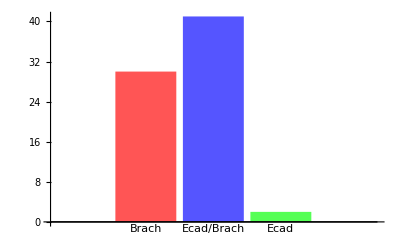

```mathematica
BarChart[Count[type,#]&/@{2,1,3},ChartStyle-> {EdgeForm[None],{Lighter@Red,Lighter@Blue,Lighter@Green}},
AxesStyle->{{Black,12},{Black,12}},ChartLabels->{"Brach","Ecad/Brach","Ecad"}]
```

```mathematica
populationCells=ecadbrach~Join~brach~Join~ecad;
```

```mathematica
polarDistcells=With[{cent=Mean@populationCells},
{
(x↦coordTrans[x-cent])/@ecadbrach,
(x↦coordTrans[x-cent])/@brach
}
];
```

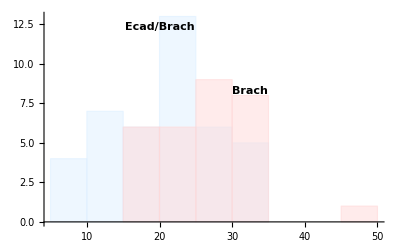

```mathematica
Histogram[polarDistcells[[All,All,1]],ChartStyle->{LightBlue,LightRed,LightGreen},ChartLabels->{Style["Ecad/Brach",Bold,Black],
Style["Brach",Bold,Black]}]
```

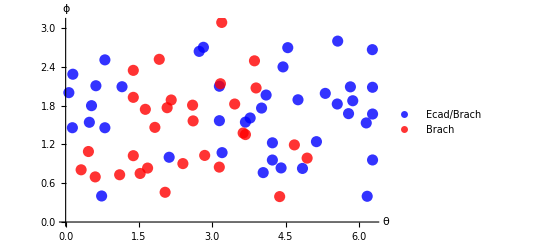

```mathematica
ListPlot[polarDistcells[[All,All,{3,2}]]/.x_/;x<0:> x+2π,
PlotStyle->{{PointSize[0.02],Opacity[0.8],Blue},{PointSize[0.02],Opacity[0.8],Red},Green},
PlotLegends->{"Ecad/Brach","Brach"},AxesLabel->(Style[#,Black,19]&/@{"θ","ϕ"}),
AxesStyle->{15,15}]
```

```mathematica
(* DelaunayMesh *)
assoc=<|Thread[ecadbrach->"EB"]~Join~Thread[brach->"B"]~Join~Thread[ecad-> "E"]|>;
pts=Join[ecadbrach,brach,ecad];
mesh=DelaunayMesh@pts
```

-Graphics3D-

```mathematica
(graph=MeshPrimitives[mesh,1]/. Line[{x_,y_}]:> UndirectedEdge[x,y] //Graph3D[#,VertexStyle->(Thread[brach-> Red]~Join~
Thread[ecad-> Green])]&)
```

-Graphics3D-

```mathematica
vertexList=VertexList[graph];
adjMat=AdjacencyMatrix[graph]
adjMat=Normal@adjMat;
```

SparseArray[…]

```mathematica
(*extract edges less than 12 units*)
GroupBy[
MapAt[#/.rules&@*Normal@*Counts@*Flatten,MapIndexed[assoc[#1]->(x↦If[EuclideanDistance[#1,x]≤12.0,Lookup[assoc,{x}],Nothing])/@Extract[vertexList,Position[adjMat[[First@#2]],1]]&,vertexList],{All,2}],
First-> Last,Counts]
```

<|EB→<|EB→34,B→7|>,B→<|B→20,EB→10|>,E→<|EB→2|>|>

```mathematica
GroupBy[
MapAt[#/.rules&,
MapIndexed[assoc[#1]->Normal@Counts@Lookup[assoc,Extract[vertexList,Position[adjMat[[First@#2]],1]]]&,vertexList],{All,2}],
First-> Last,Counts]
```

<|EB→<|B→11,EB→30|>,B→<|B→20,EB→10|>,E→<|EB→2|>|>

```mathematica
(* edge traversals *)
```

```mathematica
edgeList=EdgeList[graph];
```

```mathematica
With[{f=Map[assoc,edgeList,{2}]},
EBedgeEBpos=Position[f,"EB"<->"EB"];
BedgeBpos=Position[f,"B"<->"B"];
EedgeEpos=Position[f,"E"<->"E"];
];
```

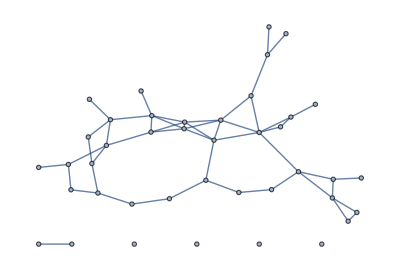

```mathematica
EBedgeEB=Extract[edgeList,EBedgeEBpos];
graphEB=Graph[VertexList[EBedgeEB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EBedgeEB]
```

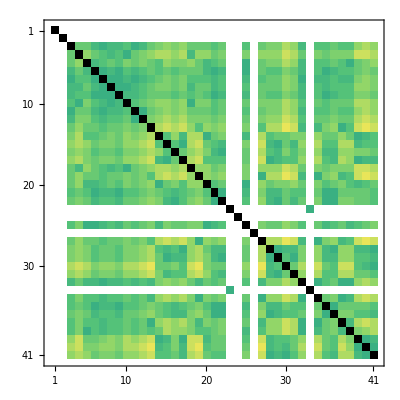

```mathematica
MatrixPlot[GraphDistanceMatrix@graphEB,ColorFunction->"BlueGreenYellow",ColorRules->{0->Black,∞->White}]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphEB]
```

{6,{35,2,1,1,1,1}}

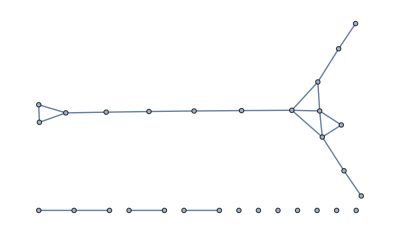

```mathematica
BedgeB=Extract[edgeList,BedgeBpos];
graphB=Graph[VertexList[BedgeB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@BedgeB]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphB]
```

{11,{16,3,2,2,1,1,1,1,1,1,1}}

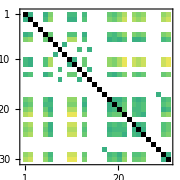

```mathematica
MatrixPlot[GraphDistanceMatrix@graphB,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
```

```mathematica
EedgeE=Extract[edgeList,EedgeEpos];
```

```mathematica
graphE=If[EedgeE≠{},
Graph[VertexList[EedgeE],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EedgeE,ImageSize->Small],
None
]
```

None

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphE]
```

{1,IGConnectedComponentSizes[None]}

```mathematica
If[EedgeE≠{},
MatrixPlot[GraphDistanceMatrix@graphE,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
]
```

## Image set 2 ✓

```mathematica
{type,slice,X,Y,V,Cpos,Z,T,Xmic,Ymic,Zmic}=Transpose@Import[setInd["2"],"Data"];
Counts[Rest@type]
```

<|1→21,2→9,4→3,3→2|>

```mathematica
{div,ecadbrach,brach,ecad}=Transpose[{Extract[Xmic,#],Extract[Ymic,#],Extract[Zmic,#]}]&/@{Position[type,4],
Position[type,1],Position[type,2],Position[type,3]};
```

```mathematica
Graphics3D[{Opacity[1],Lighter@Cyan,Sphere[#,3.5]&/@div,Lighter@Red,Sphere[#,3.5]&/@brach,Lighter@Blue,Sphere[#,3.5]&/@ecadbrach,
Lighter@Green,Sphere[#,3.5]&/@ecad},Boxed->False,ImageSize->Small,Background->None]
```

-Graphics3D-

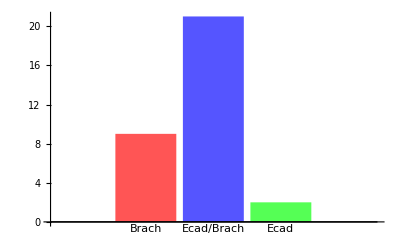

```mathematica
BarChart[Count[type,#]&/@{2,1,3},ChartStyle-> {EdgeForm[None],{Lighter@Red,Lighter@Blue,Lighter@Green}},
AxesStyle->{{Black,12},{Black,12}},ChartLabels->{"Brach","Ecad/Brach","Ecad"}]
```

## Image set 3 ✓

```mathematica
{type,slice,X,Y,V,Cpos,Z,T,Xmic,Ymic,Zmic}=Transpose@Import[setInd["3"],"Data"];
Counts[Rest@type]
```

<|2→13,1→42,3→7,4→5|>

```mathematica
{div,ecadbrach,brach,ecad}=Transpose[{Extract[Xmic,#],Extract[Ymic,#],Extract[Zmic,#]}]&/@{Position[type,4],
Position[type,1],Position[type,2],Position[type,3]};
```

```mathematica
Graphics3D[{Opacity[1],Lighter@Cyan,Sphere[#,3.5]&/@div,Lighter@Red,Sphere[#,3.5]&/@brach,Lighter@Blue,Sphere[#,3.5]&/@ecadbrach,
Lighter@Green,Sphere[#,3.5]&/@ecad},Boxed->False,ImageSize->Medium,Background->None]
```

-Graphics3D-

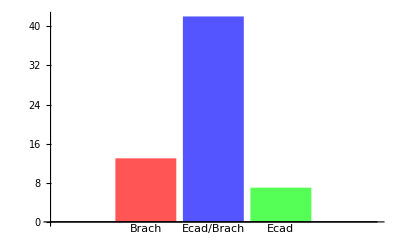

```mathematica
BarChart[Count[type,#]&/@{2,1,3},ChartStyle-> {EdgeForm[None],{Lighter@Red,Lighter@Blue,Lighter@Green}},
AxesStyle->{{Black,12},{Black,12}},ChartLabels->{"Brach","Ecad/Brach","Ecad"}]
```

```mathematica
populationCells=ecadbrach~Join~brach~Join~ecad;
```

```mathematica
polarDistcells=With[{cent=Mean@populationCells},
{
(x↦coordTrans[x-cent])/@ecadbrach,
(x↦coordTrans[x-cent])/@brach
}
];
```

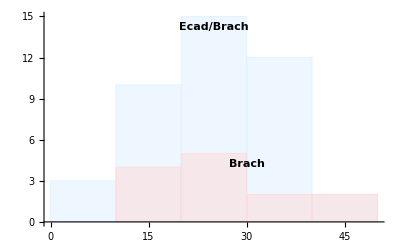

```mathematica
Histogram[polarDistcells[[All,All,1]],ChartStyle->{LightBlue,LightRed,LightGreen},ChartLabels->{Style["Ecad/Brach",Bold,Black],
Style["Brach",Bold,Black]}]
```

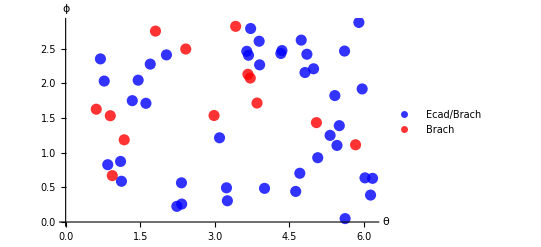

```mathematica
ListPlot[polarDistcells[[All,All,{3,2}]]/.x_/;x<0:> x+2π,
PlotStyle->{{PointSize[0.02],Opacity[0.8],Blue},{PointSize[0.02],Opacity[0.8],Red},Green},
PlotLegends->{"Ecad/Brach","Brach"},AxesLabel->(Style[#,Black,19]&/@{"θ","ϕ"}),
AxesStyle->{15,15}]
```

```mathematica
(* DelaunayMesh *)
assoc=<|Thread[ecadbrach->"EB"]~Join~Thread[brach->"B"]~Join~Thread[ecad-> "E"]|>;
pts=Join[ecadbrach,brach,ecad];
mesh=DelaunayMesh@pts
```

-Graphics3D-

```mathematica
(graph=MeshPrimitives[mesh,1]/. Line[{x_,y_}]:> UndirectedEdge[x,y] //Graph3D[#,VertexStyle->(Thread[brach-> Red]~Join~
Thread[ecad-> Green])]&)
```

-Graphics3D-

```mathematica
vertexList=VertexList[graph];
adjMat=AdjacencyMatrix[graph]
adjMat=Normal@adjMat;
```

SparseArray[…]

```mathematica
(*extract edges less than 12 units*)
GroupBy[
MapAt[#/.rules&@*Normal@*Counts@*Flatten,MapIndexed[assoc[#1]->(x↦If[EuclideanDistance[#1,x]≤12.0,Lookup[assoc,{x}],Nothing])/@Extract[vertexList,Position[adjMat[[First@#2]],1]]&,vertexList],{All,2}],
First-> Last,Counts]
```

<|EB→<|EB→38,B→3,E→1|>,B→<|EB→9,B→4|>,E→<|EB→4,E→1,B→2|>|>

```mathematica
(* edge traversals *)
```

```mathematica
edgeList=EdgeList[graph];
```

```mathematica
With[{f=Map[assoc,edgeList,{2}]},
EBedgeEBpos=Position[f,"EB"<->"EB"];
BedgeBpos=Position[f,"B"<->"B"];
EedgeEpos=Position[f,"E"<->"E"];
];
```

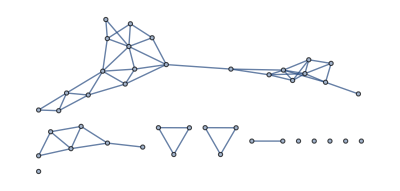

```mathematica
EBedgeEB=Extract[edgeList,EBedgeEBpos];
graphEB=Graph[VertexList[EBedgeEB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EBedgeEB]
```

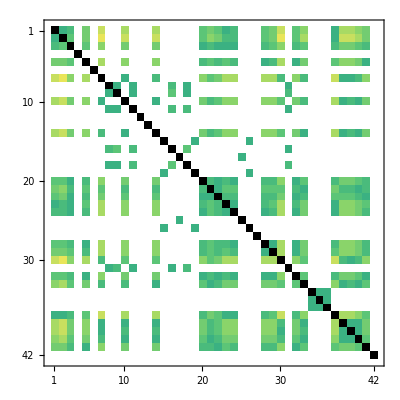

```mathematica
MatrixPlot[GraphDistanceMatrix@graphEB,ColorFunction->"BlueGreenYellow",ColorRules->{0->Black,∞->White}]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphEB]
```

{11,{22,6,3,3,2,1,1,1,1,1,1}}

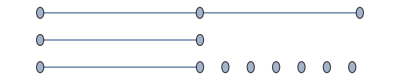

```mathematica
BedgeB=Extract[edgeList,BedgeBpos];
graphB=Graph[VertexList[BedgeB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@BedgeB]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphB]
```

{9,{3,2,2,1,1,1,1,1,1}}

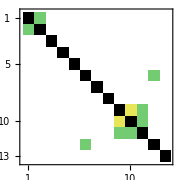

```mathematica
MatrixPlot[GraphDistanceMatrix@graphB,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
```

```mathematica
EedgeE=Extract[edgeList,EedgeEpos];
```

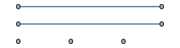

```mathematica
If[EedgeE≠{},
graphE=Graph[VertexList[EedgeE],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EedgeE,ImageSize->Small]
]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphE]
```

{5,{2,2,1,1,1}}

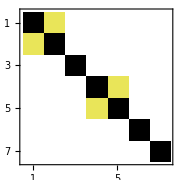

```mathematica
If[EedgeE≠{},
MatrixPlot[GraphDistanceMatrix@graphE,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
]
```

## Image set 4

```mathematica
{type,slice,X,Y,V,Cpos,Z,T,Xmic,Ymic,Zmic}=Transpose@Import[setInd["4"],"Data"];
Counts[Rest@type]
```

<|2→23,1→9,3→24|>

```mathematica
{div,ecadbrach,brach,ecad}=Transpose[{Extract[Xmic,#],Extract[Ymic,#],Extract[Zmic,#]}]&/@{Position[type,1],
Position[type,2],Position[type,3],Position[type,4]};
```

```mathematica
Graphics3D[{Opacity[1],Lighter@Cyan,Sphere[#,3.5]&/@div,Lighter@Red,Sphere[#,3.5]&/@brach,Lighter@Blue,Sphere[#,3.5]&/@ecadbrach},Boxed->False,ImageSize->Medium,Background->None]
```

-Graphics3D-

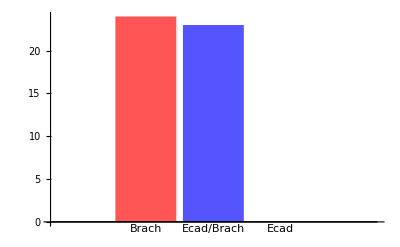

```mathematica
BarChart[Count[type,#]&/@{3,2,4},ChartStyle-> {EdgeForm[None],{Lighter@Red,Lighter@Blue,Lighter@Green}},
AxesStyle->{{Black,12},{Black,12}},ChartLabels->{"Brach","Ecad/Brach","Ecad"}]
```

## Image set 5 ✓

```mathematica
{type,slice,X,Y,V,Cpos,Z,T,Xmic,Ymic,Zmic}=Transpose@Import[setInd["5"],"Data"];
Counts[Rest@type]
```

<|4→9,2→39,1→84,3→3|>

```mathematica
{div,ecadbrach,brach,ecad}=Transpose[{Extract[Xmic,#],Extract[Ymic,#],Extract[Zmic,#]}]&/@{Position[type,4],
Position[type,1],Position[type,2],Position[type,3]};
```

```mathematica
Graphics3D[{Opacity[1],Lighter@Cyan,Sphere[#,3.5]&/@div,Lighter@Red,Sphere[#,3.5]&/@brach,Lighter@Blue,Sphere[#,3.5]&/@ecadbrach,
Lighter@Green,Sphere[#,3.5]&/@ecad},Boxed->True,ImageSize->Medium,Background->None]
```

-Graphics3D-

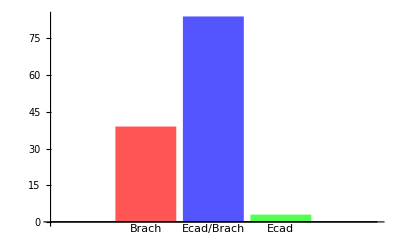

```mathematica
BarChart[Count[type,#]&/@{2,1,3},ChartStyle-> {EdgeForm[None],{Lighter@Red,Lighter@Blue,Lighter@Green}},
AxesStyle->{{Black,12},{Black,12}},ChartLabels->{"Brach","Ecad/Brach","Ecad"}]
```

```mathematica
populationCells=ecadbrach~Join~brach~Join~ecad;
```

```mathematica
polarDistcells=With[{cent=Mean@populationCells},
{
(x↦coordTrans[x-cent])/@ecadbrach,
(x↦coordTrans[x-cent])/@brach
}
];
```

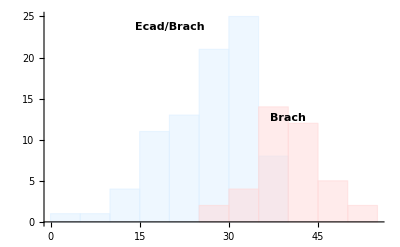

```mathematica
Histogram[polarDistcells[[All,All,1]],ChartStyle->{LightBlue,LightRed,LightGreen},ChartLabels->{Style["Ecad/Brach",Bold,Black],
Style["Brach",Bold,Black]}]
```

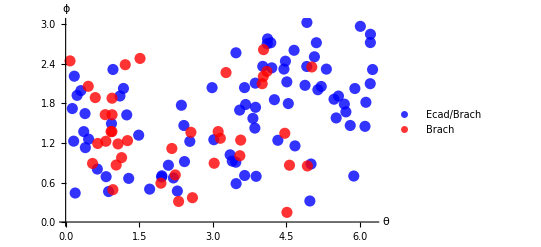

```mathematica
ListPlot[polarDistcells[[All,All,{3,2}]]/.x_/;x<0:> x+2π,
PlotStyle->{{PointSize[0.02],Opacity[0.8],Blue},{PointSize[0.02],Opacity[0.8],Red},Green},
PlotLegends->{"Ecad/Brach","Brach"},AxesLabel->(Style[#,Black,19]&/@{"θ","ϕ"}),
AxesStyle->{15,15}]
```

```mathematica
(* DelaunayMesh *)
assoc=<|Thread[ecadbrach->"EB"]~Join~Thread[brach->"B"]~Join~Thread[ecad-> "E"]|>;
pts=Join[ecadbrach,brach,ecad];
mesh=DelaunayMesh@pts
```

-Graphics3D-

```mathematica
(graph=MeshPrimitives[mesh,1]/. Line[{x_,y_}]:> UndirectedEdge[x,y] //Graph3D[#,VertexStyle->(Thread[brach-> Red]~Join~
Thread[ecad-> Green])]&)
```

-Graphics3D-

```mathematica
vertexList=VertexList[graph];
adjMat=AdjacencyMatrix[graph]
adjMat=Normal@adjMat;
```

SparseArray[…]

```mathematica
(*extract edges less than 12 units*)
GroupBy[
MapAt[#/.rules&@*Normal@*Counts@*Flatten,MapIndexed[assoc[#1]->(x↦If[EuclideanDistance[#1,x]≤12.0,Lookup[assoc,{x}],Nothing])/@Extract[vertexList,Position[adjMat[[First@#2]],1]]&,vertexList],{All,2}],
First-> Last,Counts]
```

<|EB→<|EB→76,E→2,B→6|>,B→<|EB→15,B→23,E→1|>,E→<|EB→3|>|>

```mathematica
(* edge traversals *)
```

```mathematica
edgeList=EdgeList[graph];
```

```mathematica
With[{f=Map[assoc,edgeList,{2}]},
EBedgeEBpos=Position[f,"EB"<->"EB"];
BedgeBpos=Position[f,"B"<->"B"];
EedgeEpos=Position[f,"E"<->"E"];
];
```

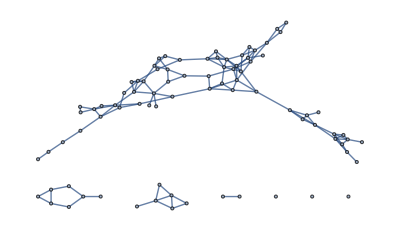

```mathematica
EBedgeEB=Extract[edgeList,EBedgeEBpos];
graphEB=Graph[VertexList[EBedgeEB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EBedgeEB]
```

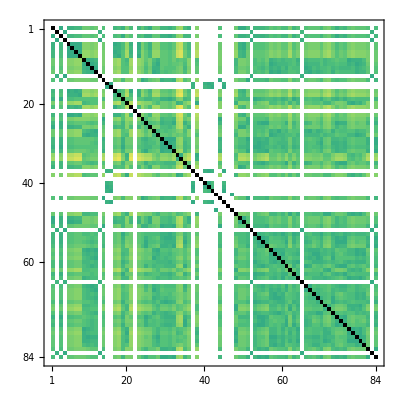

```mathematica
MatrixPlot[GraphDistanceMatrix@graphEB,ColorFunction->"BlueGreenYellow",ColorRules->{0->Black,∞->White}]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphEB]
```

{7,{66,7,6,2,1,1,1}}

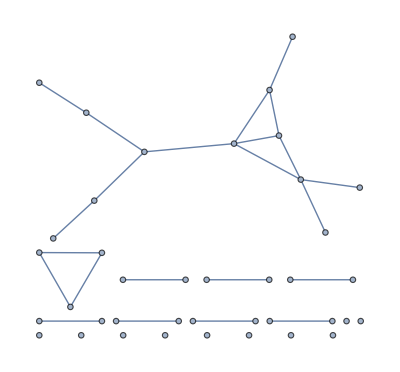

```mathematica
BedgeB=Extract[edgeList,BedgeBpos];
graphB=Graph[VertexList[BedgeB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@BedgeB]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphB]
```

{19,{12,3,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1}}

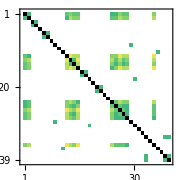

```mathematica
MatrixPlot[GraphDistanceMatrix@graphB,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
```

```mathematica
EedgeE=Extract[edgeList,EedgeEpos];
```

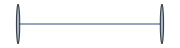

```mathematica
If[EedgeE≠{},
graphE=Graph[VertexList[EedgeE],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EedgeE,ImageSize->Small]
]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphE]
```

{1,{2}}

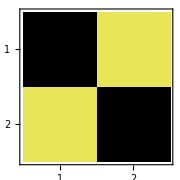

```mathematica
If[EedgeE≠{},
MatrixPlot[GraphDistanceMatrix@graphE,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
]
```

## Image set 6 ✓

```mathematica
{type,slice,X,Y,V,Cpos,Z,T,Xmic,Ymic,Zmic}=Transpose@Import[setInd["6"],"Data"];
Counts[Rest@type]
```

<|1→81,2→31,3→4,4→2|>

```mathematica
{div,ecadbrach,brach,ecad}=Transpose[{Extract[Xmic,#],Extract[Ymic,#],Extract[Zmic,#]}]&/@{Position[type,4],
Position[type,1],Position[type,2],Position[type,3]};
```

```mathematica
Graphics3D[{Opacity[1],Lighter@Cyan,Sphere[#,3.5]&/@div,Lighter@Red,Sphere[#,3.5]&/@brach,Lighter@Blue,Sphere[#,3.5]&/@ecadbrach,
Lighter@Green,Sphere[#,3.5]&/@ecad},Boxed->False,ImageSize->Medium,Background->None]
```

-Graphics3D-

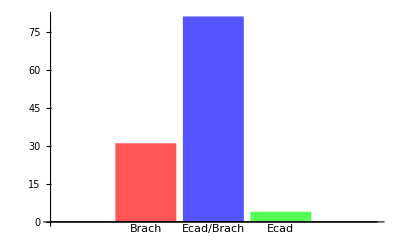

```mathematica
BarChart[Count[type,#]&/@{2,1,3},ChartStyle-> {EdgeForm[None],{Lighter@Red,Lighter@Blue,Lighter@Green}},
AxesStyle->{{Black,12},{Black,12}},ChartLabels->{"Brach","Ecad/Brach","Ecad"}]
```

```mathematica
populationCells=ecadbrach~Join~brach~Join~ecad;
```

```mathematica
polarDistcells=With[{cent=Mean@populationCells},
{
(x↦coordTrans[x-cent])/@ecadbrach,
(x↦coordTrans[x-cent])/@brach
}
];
```

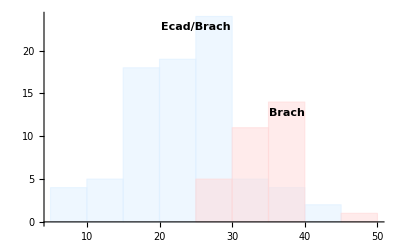

```mathematica
Histogram[polarDistcells[[All,All,1]],ChartStyle->{LightBlue,LightRed,LightGreen},ChartLabels->{Style["Ecad/Brach",Bold,Black],
Style["Brach",Bold,Black]}]
```

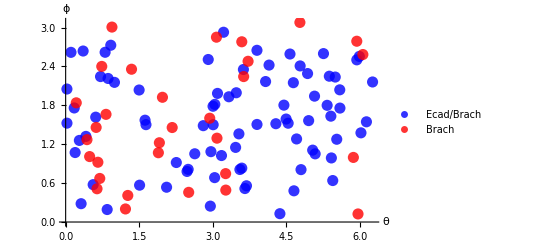

```mathematica
ListPlot[polarDistcells[[All,All,{3,2}]]/.x_/;x<0:> x+2π,
PlotStyle->{{PointSize[0.02],Opacity[0.8],Blue},{PointSize[0.02],Opacity[0.8],Red},Green},
PlotLegends->{"Ecad/Brach","Brach"},AxesLabel->(Style[#,Black,19]&/@{"θ","ϕ"}),
AxesStyle->{15,15}]
```

```mathematica
(* DelaunayMesh *)
assoc=<|Thread[ecadbrach->"EB"]~Join~Thread[brach->"B"]~Join~Thread[ecad-> "E"]|>;
pts=Join[ecadbrach,brach,ecad];
mesh=DelaunayMesh@pts
```

-Graphics3D-

```mathematica
(graph=MeshPrimitives[mesh,1]/. Line[{x_,y_}]:> UndirectedEdge[x,y] //Graph3D[#,VertexStyle->(Thread[brach-> Red]~Join~
Thread[ecad-> Green])]&)
```

-Graphics3D-

```mathematica
vertexList=VertexList[graph];
adjMat=AdjacencyMatrix[graph]
adjMat=Normal@adjMat;
```

SparseArray[…]

```mathematica
(*extract edges less than 12 units*)
GroupBy[
MapAt[#/.rules&@*Normal@*Counts@*Flatten,MapIndexed[assoc[#1]->(x↦If[EuclideanDistance[#1,x]≤12.0,Lookup[assoc,{x}],Nothing])/@Extract[vertexList,Position[adjMat[[First@#2]],1]]&,vertexList],{All,2}],
First-> Last,Counts]
```

<|EB→<|EB→72,B→9|>,B→<|B→20,EB→11|>,E→<|EB→4|>|>

```mathematica
(* edge traversals *)
```

```mathematica
edgeList=EdgeList[graph];
```

```mathematica
With[{f=Map[assoc,edgeList,{2}]},
EBedgeEBpos=Position[f,"EB"<->"EB"];
BedgeBpos=Position[f,"B"<->"B"];
EedgeEpos=Position[f,"E"<->"E"];
];
```

```mathematica
EBedgeEB=Extract[edgeList,EBedgeEBpos];
```

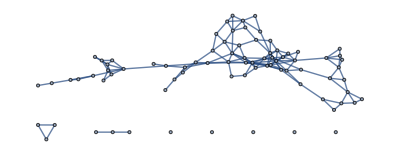

```mathematica
graphEB=Graph[VertexList[EBedgeEB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EBedgeEB]
```

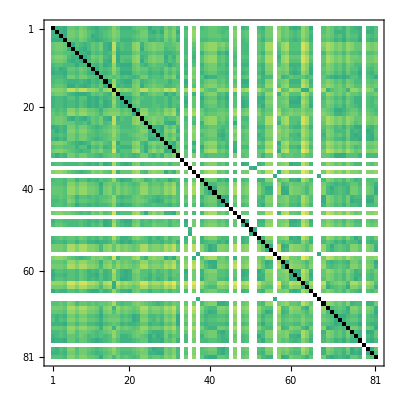

```mathematica
MatrixPlot[GraphDistanceMatrix@graphEB,ColorFunction->"BlueGreenYellow",ColorRules->{0->Black,∞->White}]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphEB]
```

{8,{70,3,3,1,1,1,1,1}}

```mathematica
BedgeB=Extract[edgeList,BedgeBpos];
```

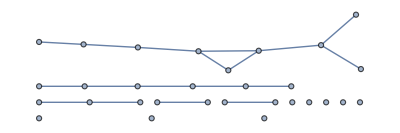

```mathematica
graphB=Graph[VertexList[BedgeB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@BedgeB]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphB]
```

{13,{9,6,3,2,2,1,1,1,1,1,1,1,1}}

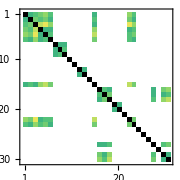

```mathematica
MatrixPlot[GraphDistanceMatrix@graphB,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
```

```mathematica
EedgeE=Extract[edgeList,EedgeEpos];
```

```mathematica
If[EedgeE≠{},
graphE=Graph[VertexList[EedgeE],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EedgeE,ImageSize->Small]
]
```

-Graphics-

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphE]
```

{3,{1,1,1}}

```mathematica
If[EedgeE≠{},
MatrixPlot[GraphDistanceMatrix@graphE,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
]
```

-Graphics-

## Image set 7 ✓

```mathematica
{type,slice,X,Y,V,Cpos,Z,T,Xmic,Ymic,Zmic}=Transpose@Import[setInd["7"],"Data"];
Counts@Rest[type]
```

<|1→76,2→44,3→1,4→2|>

```mathematica
{div,ecadbrach,brach,ecad}=Transpose[{Extract[Xmic,#],Extract[Ymic,#],Extract[Zmic,#]}]&/@{Position[type,4],
Position[type,1],Position[type,2],Position[type,3]};
```

```mathematica
Graphics3D[{Opacity[1],Lighter@Cyan,Sphere[#,3.5]&/@div,Lighter@Red,Sphere[#,3.5]&/@brach,Lighter@Blue,Sphere[#,3.5]&/@ecadbrach,
Lighter@Green,Sphere[#,3.5]&/@ecad},Boxed->False,ImageSize->Medium,Background->None]
```

-Graphics3D-

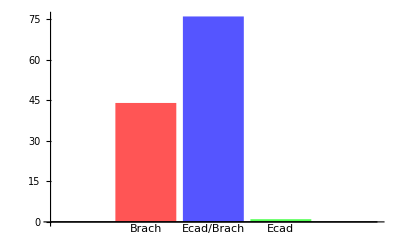

```mathematica
BarChart[Count[type,#]&/@{2,1,3},ChartStyle-> {EdgeForm[None],{Lighter@Red,Lighter@Blue,Lighter@Green}},
AxesStyle->{{Black,12},{Black,12}},ChartLabels->{"Brach","Ecad/Brach","Ecad"}]
```

```mathematica
populationCells=ecadbrach~Join~brach~Join~ecad;
```

```mathematica
polarDistcells=With[{cent=Mean@populationCells},
{
(x↦coordTrans[x-cent])/@ecadbrach,
(x↦coordTrans[x-cent])/@brach
}
];
```

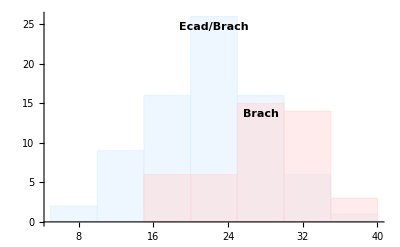

```mathematica
Histogram[polarDistcells[[All,All,1]],ChartStyle->{LightBlue,LightRed,LightGreen},ChartLabels->{Style["Ecad/Brach",Bold,Black],
Style["Brach",Bold,Black]}]
```

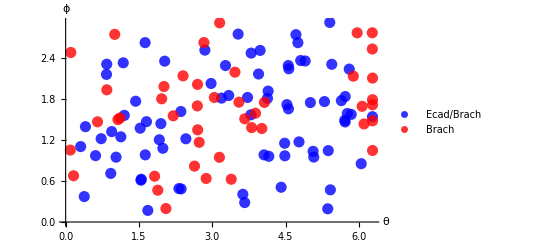

```mathematica
ListPlot[polarDistcells[[All,All,{3,2}]]/.x_/;x<0:> x+2π,
PlotStyle->{{PointSize[0.02],Opacity[0.8],Blue},{PointSize[0.02],Opacity[0.8],Red},Green},
PlotLegends->{"Ecad/Brach","Brach"},AxesLabel->(Style[#,Black,19]&/@{"θ","ϕ"}),
AxesStyle->{15,15}]
```

```mathematica
(* DelaunayMesh *)
assoc=<|Thread[ecadbrach->"EB"]~Join~Thread[brach->"B"]~Join~Thread[ecad-> "E"]|>;
pts=Join[ecadbrach,brach,ecad];
mesh=DelaunayMesh@pts
```

-Graphics3D-

```mathematica
(graph=MeshPrimitives[mesh,1]/. Line[{x_,y_}]:> UndirectedEdge[x,y] //Graph3D[#,VertexStyle->(Thread[brach-> Red]~Join~
Thread[ecad-> Green])]&)
```

-Graphics3D-

```mathematica
vertexList=VertexList[graph];
adjMat=AdjacencyMatrix[graph]
adjMat=Normal@adjMat;
```

SparseArray[…]

```mathematica
(*extract edges less than 12 units*)
GroupBy[
MapAt[#/.rules&@*Normal@*Counts@*Flatten,MapIndexed[assoc[#1]->(x↦If[EuclideanDistance[#1,x]≤12.0,Lookup[assoc,{x}],Nothing])/@Extract[vertexList,Position[adjMat[[First@#2]],1]]&,vertexList],{All,2}],
First-> Last,Counts]
```

<|EB→<|EB→68,B→8|>,B→<|B→23,EB→20,E→1|>,E→<|B→1|>|>

```mathematica
(* edge traversals *)
```

```mathematica
edgeList=EdgeList[graph];
```

```mathematica
With[{f=Map[assoc,edgeList,{2}]},
EBedgeEBpos=Position[f,"EB"<->"EB"];
BedgeBpos=Position[f,"B"<->"B"];
EedgeEpos=Position[f,"E"<->"E"];
];
```

```mathematica
EBedgeEB=Extract[edgeList,EBedgeEBpos];
```

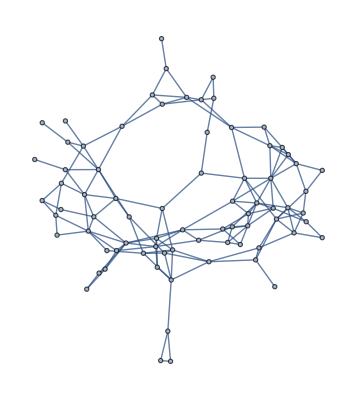

```mathematica
graphEB=Graph[VertexList[EBedgeEB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EBedgeEB]
```

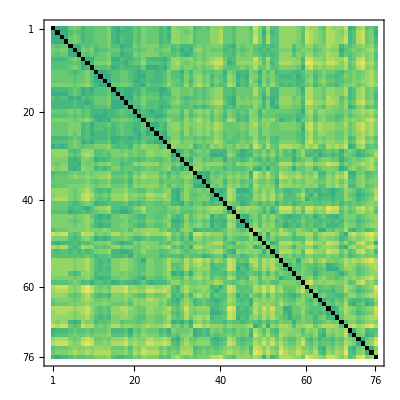

```mathematica
MatrixPlot[GraphDistanceMatrix@graphEB,ColorFunction->"BlueGreenYellow",ColorRules->{0->Black,∞->White}]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphEB]
```

{1,{76}}

```mathematica
BedgeB=Extract[edgeList,BedgeBpos];
```

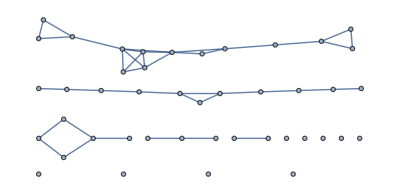

```mathematica
graphB=Graph[VertexList[BedgeB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@BedgeB]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphB]
```

{14,{14,11,5,3,2,1,1,1,1,1,1,1,1,1}}

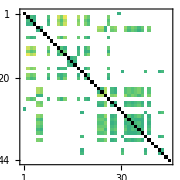

```mathematica
MatrixPlot[GraphDistanceMatrix@graphB,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
```

```mathematica
EedgeE=Extract[edgeList,EedgeEpos]
```

{}

```mathematica
If[EedgeE≠{},
graphE=Graph[VertexList[EedgeE],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EedgeE],
graphE=None
]
```

None

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphE]
```

{1,IGConnectedComponentSizes[None]}

```mathematica
If[EedgeE≠{},
MatrixPlot[GraphDistanceMatrix@graphE,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
]
```

## Image set 8 ✓

```mathematica
{type,slice,X,Y,V,Cpos,Z,T,Xmic,Ymic,Zmic}=Transpose@Import[setInd["8"],"Data"];
Counts@Rest[type]
```

<|1→67,2→25,3→10,4→4|>

```mathematica
{div,ecadbrach,brach,ecad}=Transpose[{Extract[Xmic,#],Extract[Ymic,#],Extract[Zmic,#]}]&/@{Position[type,4],
Position[type,1],Position[type,2],Position[type,3]};
```

```mathematica
Graphics3D[{Opacity[1],Lighter@Cyan,Sphere[#,3.5]&/@div,Lighter@Red,Sphere[#,3.5]&/@brach,Lighter@Blue,Sphere[#,3.5]&/@ecadbrach,
Lighter@Green,Sphere[#,3.5]&/@ecad},Boxed->False,ImageSize->Medium,Background->None]
```

-Graphics3D-

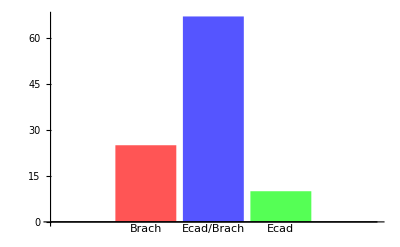

```mathematica
BarChart[Count[type,#]&/@{2,1,3},ChartStyle-> {EdgeForm[None],{Lighter@Red,Lighter@Blue,Lighter@Green}},
AxesStyle->{{Black,12},{Black,12}},ChartLabels->{"Brach","Ecad/Brach","Ecad"}]
```

```mathematica
populationCells=ecadbrach~Join~brach~Join~ecad;
```

```mathematica
polarDistcells=With[{cent=Mean@populationCells},
{
(x↦coordTrans[x-cent])/@ecadbrach,
(x↦coordTrans[x-cent])/@brach
}
];
```

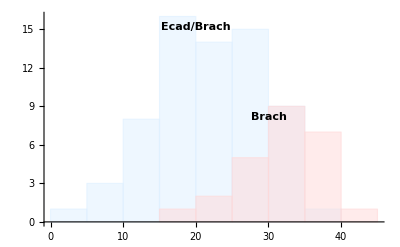

```mathematica
Histogram[polarDistcells[[All,All,1]],ChartStyle->{LightBlue,LightRed,LightGreen},ChartLabels->{Style["Ecad/Brach",Bold,Black],
Style["Brach",Bold,Black]}]
```

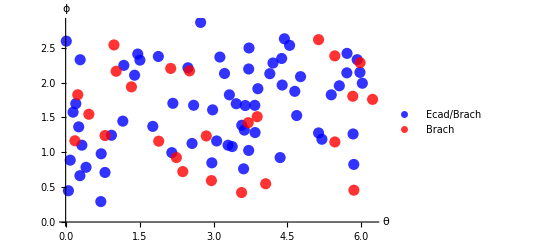

```mathematica
ListPlot[polarDistcells[[All,All,{3,2}]]/.x_/;x<0:> x+2π,
PlotStyle->{{PointSize[0.02],Opacity[0.8],Blue},{PointSize[0.02],Opacity[0.8],Red},Green},
PlotLegends->{"Ecad/Brach","Brach"},AxesLabel->(Style[#,Black,19]&/@{"θ","ϕ"}),
AxesStyle->{15,15}]
```

```mathematica
(* DelaunayMesh *)
assoc=<|Thread[ecadbrach->"EB"]~Join~Thread[brach->"B"]~Join~Thread[ecad-> "E"]|>;
pts=Join[ecadbrach,brach,ecad];
mesh=DelaunayMesh@pts
```

-Graphics3D-

```mathematica
(graph=MeshPrimitives[mesh,1]/. Line[{x_,y_}]:> UndirectedEdge[x,y] //Graph3D[#,VertexStyle->(Thread[brach-> Red]~Join~
Thread[ecad-> Green])]&)
```

-Graphics3D-

```mathematica
vertexList=VertexList[graph];
adjMat=AdjacencyMatrix[graph]
adjMat=Normal@adjMat;
```

SparseArray[…]

```mathematica
(*extract edges less than 12 units*)
GroupBy[
MapAt[#/.rules&@*Normal@*Counts@*Flatten,MapIndexed[assoc[#1]->(x↦If[EuclideanDistance[#1,x]≤12.0,Lookup[assoc,{x}],Nothing])/@Extract[vertexList,Position[adjMat[[First@#2]],1]]&,vertexList],{All,2}],
First-> Last,Counts]
```

<|EB→<|EB→60,B→7|>,B→<|B→8,EB→17|>,E→<|EB→8,B→2|>|>

```mathematica
(*GroupBy[
MapAt[#/.rules&,
MapIndexed[assoc[#1]->Normal@Counts@Lookup[assoc,Extract[vertexList,Position[adjMat[[First@#2]],1]]]&,vertexList],{All,2}],
First-> Last,Counts]*)
```

```mathematica
(* edge traversals *)
```

```mathematica
edgeList=EdgeList[graph];
```

```mathematica
With[{f=Map[assoc,edgeList,{2}]},
EBedgeEBpos=Position[f,"EB"<->"EB"];
BedgeBpos=Position[f,"B"<->"B"];
EedgeEpos=Position[f,"E"<->"E"];
];
```

```mathematica
EBedgeEB=Extract[edgeList,EBedgeEBpos];
```

```mathematica
(*
graphEBedgeEB=Graph[EBedgeEB,EdgeWeight->(EuclideanDistance@@#&/@EBedgeEB)];
MatrixPlot[GraphDistanceMatrix@graphEBedgeEB,ColorFunction->"BlueGreenYellow"];
MeanGraphDistance[graphEBedgeEB];
*)
```

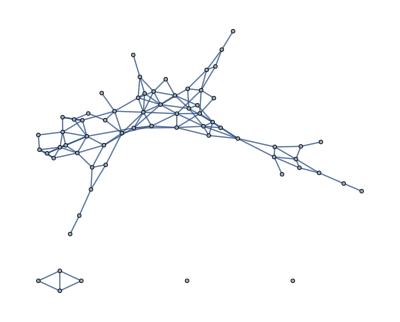

```mathematica
graphEB=Graph[VertexList[EBedgeEB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EBedgeEB]
```

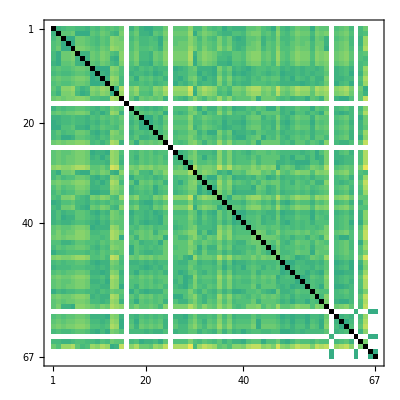

```mathematica
MatrixPlot[GraphDistanceMatrix@graphEB,ColorFunction->"BlueGreenYellow",ColorRules->{0->Black,∞->White}]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphEB]
```

{4,{61,4,1,1}}

```mathematica
BedgeB=Extract[edgeList,BedgeBpos];
```

```mathematica
(*
graphBedgeB=Graph[BedgeB,EdgeWeight->(EuclideanDistance@@#&/@BedgeB)]
MatrixPlot[GraphDistanceMatrix@graphBedgeB,ColorFunction->"BlueGreenYellow"]
MeanGraphDistance[graphBedgeB]
*)
```

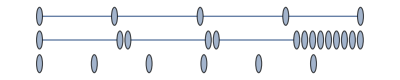

```mathematica
graphB=Graph[VertexList[BedgeB],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@BedgeB]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphB]
```

{18,{5,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

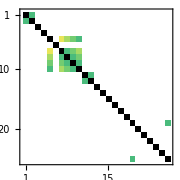

```mathematica
MatrixPlot[GraphDistanceMatrix@graphB,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
```

```mathematica
EedgeE=Extract[edgeList,EedgeEpos];
```

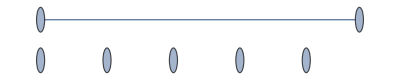

```mathematica
graphE=Graph[VertexList[EedgeE],If[Apply[EuclideanDistance,#]≤12,#,Nothing]&/@EedgeE]
```

```mathematica
{Length[#],#}&@IGConnectedComponentSizes[graphE]
```

{6,{2,1,1,1,1,1}}

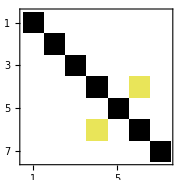

```mathematica
MatrixPlot[GraphDistanceMatrix@graphE,ColorFunction->"BlueGreenYellow",ColorRules->{0-> Black,Infinity-> White},
ImageSize->Small]
```

## Plots

#### Misc

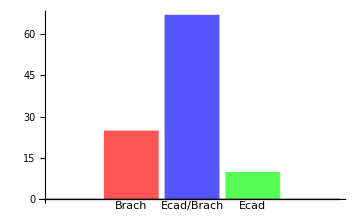
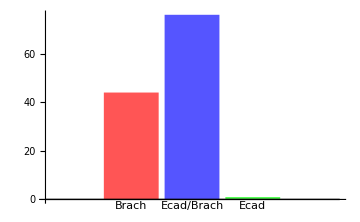
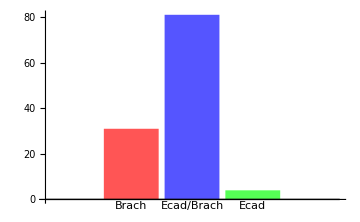
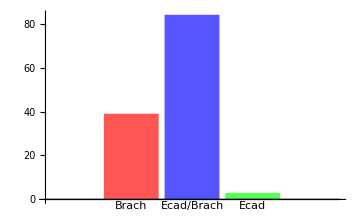
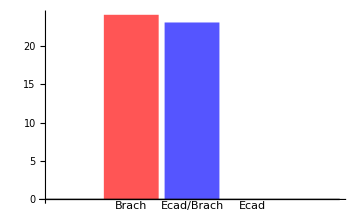
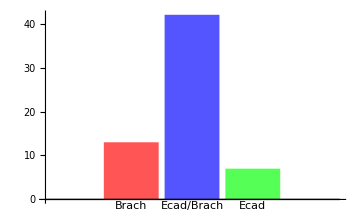
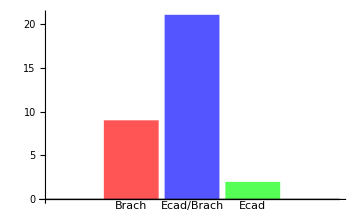
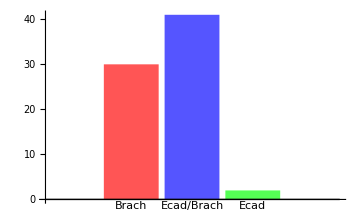
```mathematica
Grid[ArrayReshape[Framed/@Values@{8-> -Graphics-,7->-Graphics-,6->-Graphics-,5->-Graphics-,4->-Graphics-,3->-Graphics-,2-> -Graphics-,1->-Graphics-},{4,2}],Spacings->{5,1}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

#### plots

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\analysis notebooks\\spatial organization of cell population\\CellPopulationDist.mx"];
```

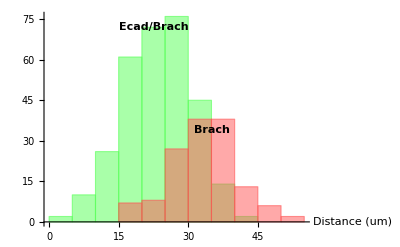

```mathematica
Histogram[{Flatten@polarRep[[All,1,All,1]],Flatten@polarRep[[All,2,All,1]]},ChartStyle->{Lighter@Green,Lighter@Red},ChartLabels->{Style["Ecad/Brach",Bold,Black],
Style["Brach",Bold,Black]},AxesLabel->{Style["Distance (um)",Bold,Black,12],None}]
```

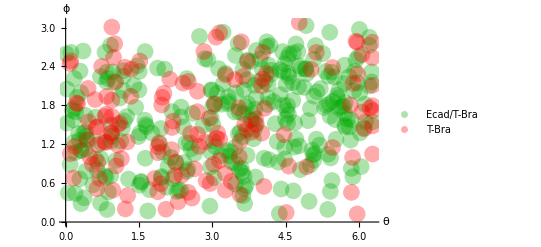

```mathematica
ListPlot[{Flatten[polarRep[[All,1,All,{3,2}]],1]/.x_/;x<0 :> x+2π,
Flatten[polarRep[[All,-1,All,{3,2}]],1]/.x_/;x<0 :> x+2π},
PlotStyle->{{PointSize[0.03],Opacity[0.33],Darker@Green},{PointSize[0.03],Opacity[0.33],Red}},
PlotLegends->{"Ecad/T-Bra","T-Bra"},AxesLabel->(Style[#,Black,19]&/@{"θ","ϕ"}),
AxesStyle->{15,15}]
```

#### Neighbourhood type

```mathematica
Echo@Style[identity,Bold,Black,FontSize->14,Background->LightBlue];
```

{<|EB→<|EB→60,B→7|>,B→<|B→8,EB→17|>,E→<|EB→8,B→2|>|>,<|EB→<|EB→68,B→8|>,B→<|B→23,EB→20,E→1|>,E→<|B→1|>|>,<|EB→<|EB→72,B→9|>,B→<|B→20,EB→11|>,E→<|EB→4|>|>,<|EB→<|EB→76,E→2,B→6|>,B→<|EB→15,B→23,E→1|>,E→<|EB→3|>|>}

```mathematica
ids=<|(First@*Union@*Keys@# -> Merge[Values@#,Total])&/@Transpose@Normal@Map[Function[x,
If[Head[#]=!={},Append[x,#],x]&@Thread[Complement[{"EB","B","E"},Keys@x]-> 0]
],identity,{2}]|>
```

<|EB→<|EB→276,B→30,E→2|>,B→<|B→74,EB→63,E→2|>,E→<|EB→15,B→3,E→0|>|>

```mathematica
(*EB cells are homotypic i.e. an EB cell is surrounded by mostly EB cells*)
```

```mathematica
N[(#EB/Total[#])]&[ids["EB"]]
```

0.896104

```mathematica
(*B cells are heterotypic*)
```

```mathematica
N[(#B/Total[#])]&[ids["B"]]
```

0.532374

```mathematica
(*E cells are surrounded by mostly EB cells *)
```

```mathematica
N[(#EB/Total[#])]&[ids["E"]]
```

0.833333

```mathematica
With[{keys=Keys@ids},
Style[
TableForm[Transpose[Outer[NumberForm[N[#2[#1]/Total[#2]]*100,3]&,keys,First[Values/@{ids}]]],
TableHeadings->ConstantArray[MapThread[Style[#1,#2,Bold,19]&,{keys,{Blue,Red,Darker@Green}}],2]],
Black,Bold,14,Background->GrayLevel[0.75]
]
]
```

| EB | B | E
EB | 89.6 | 9.74 | 0.649
B | 45.3 | 53.2 | 1.44
E | 83.3 | 16.7 | 0.

#### Connected Components

```mathematica
(*Ecad/Brachyury (EB) cells have on average 5 simply connected components*)
```

```mathematica
sccEB=Transpose[connectedcomponentsList][[1,All,1]]//Round@*N@*Mean
```

5

```mathematica
(*for EB cells the largest simply connected component on avg is 68 cells in size *)
```

```mathematica
largestComponentFracEB=Transpose[connectedcomponentsList][[1,All,-1,1]]//N@*Mean
```

68.25

```mathematica
(*Brachyury only cells (B) have on average 16 simply connected components. B cells are more fragmented *)
```

```mathematica
sccB=Transpose[connectedcomponentsList][[2,All,1]]//Round@*N@*Mean
```

16

```mathematica
(* the largest simply connected component of brachyury cells is only 10 units *)
```

```mathematica
largestComponentFracB=Transpose[connectedcomponentsList][[2,All,-1,1]]//N@*Mean
```

10.

```mathematica
Style[
TableForm[(Map[Style[#,Bold]&,{{sccEB,largestComponentFracEB/100},{sccB,largestComponentFracB/100}},{2}]),TableHeadings-> {MapThread[Style[##,Bold,18]&,{{"EB","B"},{Blue,Red}}],
Style[#,Bold,15]&/@{"Simply Connected Component","largest component fraction"}}],14,Background->GrayLevel[0.75]
]
```

| Simply Connected Component | largest component fraction
EB | 5 | 0.6825
B | 16 | 0.1